# Training iterated protocols for distillation of GHZ states with variational quantum algorithms

## Description of notebook

Author: Aron Rozgonyi - rozgonyi.aron@wigner.hu
Corresponding article: https://doi.org/10.48550/arXiv.2311.04646

In this notebook:
* simulate 3-qubit entangled state distillation protocol
* using VQA, train a quantum circuit that vanishes the noise from a noisy initial GHZ state  
* initial state is a noisy (mixed) GHZ state - 2 copies: an original and an identical copy called “flag qubits”
* 3 parties: A,B,C each of them has 1-1 qubits from original and flag qubit sets

GHZ distillation protocol steps: 
prepare parametric quantum circuit (ansatz) that consists of 3 CNOTs and single-qubit rotations (X, Z)
trainable parameters: angle of rotations (single qubit gates)
each parties perform identical operations in the circuit 
then all of them perform measurements in Z-basis on their flag qubit
on classical channel they discuss and post select the results so that they accept cases when all of them measured ‘0’  outcomes otherwise they cancel the protocol and start over
in case of successful round they perform the 2nd iteration and so on

code steps:
0) defining used operators and functions
i) creating an initial density matrix of 2 identical noisy-GHZ states;		basis: |q1,q2,q3> x |q4,q5,q6>
considering white noise the initial state: 	ρ0 = (1-λ)GHZGHZ+ λ/8 Ι 
ii) defining the quantum circuit ansatz (containing measurements) and the protocol:		circuit[_]
iii) writing a function that iterates the protocol and returns with the normalized density matrix: 	 ItC[_]
iv) defining the loss function: fidelity with GHZ state: 	loss[_]
v) defining a stochastic gradient descent optimizer for VQA: 		StochasticGradientDescent[]

-Graphics-

## Definitions

```mathematica
(* Pauli operators *)
Ι=PauliMatrix[0];
X=PauliMatrix[1];
Y=PauliMatrix[2];
Z=PauliMatrix[3];

(* Measurement projectors *)
M0=Outer[Times, {1,0},Conjugate[{1,0}]];
M=KroneckerProduct@@{Ι,M0,Ι,M0,Ι,M0};
M′=SparseArray[KroneckerProduct@@{Ι,Ι,Ι,M0,M0,M0}];
M1=Outer[Times, {0,1},Conjugate[{0,1}]];
M′1=KroneckerProduct@@{Ι,Ι,Ι,M1,M1,M1};

(* GHZ State *)
S0={1,0};
S1={0,1};
GHZ=N@(Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1])/Sqrt[2];
GHZL=N@(Flatten@KroneckerProduct[S0,S0,S0]+0.3*Flatten@KroneckerProduct[S1,S1,S1])/Sqrt[2];
ρGHZ=SparseArray@Outer[Times, GHZ,Conjugate[GHZ]];
ρGHZL=SparseArray@Outer[Times, GHZL,Conjugate[GHZL]];

(* I_2 noise *)
NoiseMatrix[Ν′_]:=ReplacePart[Table[0,{i,Ν′},{j,Ν′}],{{1,1}->1,{Ν′,Ν′}->1}]

(* parametric gates *)
Rθ[θ_,Y_]:=MatrixExp[-ⅈ*θ/2 Y]
CU[i_->j_,U_]:=MatrixExp[ⅈ/2*(Apply[KroneckerProduct,ReplacePart[{Ι,Ι,Ι,Ι,Ι,Ι},{i->Ι-Z,j->-ⅈ*MatrixLog[U]}]])]

(* CNOT gate *)
Ν=6;
basis=Tuples[{0,1},Ν];
basisS=Map["|"<>StringJoin[Map[ToString[#]&,#]]<>"⟩"&,Tuples[{0,1},Ν]];
CNOTket[i_,j_,list_]:=Block[{output=list},If[list⟦i⟧==0,output,output⟦j⟧=-output⟦j⟧+1;output]]
CNOTmatrix[i_,j_]:=Normal[SparseArray[Table[{n,Position[basis,CNOTket[i,j,basis⟦n⟧]]⟦1,1⟧}->1,{n,Length[basis]}],{Length[basis],Length[basis]}]]
Do[CNOT[i->j]=CNOTmatrix[i,j],{i,Ν},{j,Ν}]

(* SWAP GATE *)
Ν=6;
basis=Tuples[{0,1},Ν];
basisS=Map["|"<>StringJoin[Map[ToString[#]&,#]]<>"⟩"&,Tuples[{0,1},Ν]];
SWAP[i_,j_]:=Normal[SparseArray[Table[1+{k,
If[
Mod[Quotient[k,2^(Ν-i)],2]==Mod[Quotient[k,2^(Ν-j)],2],
k,
BitXor[BitXor[k,2^(Ν-i)],2^(Ν-j)]
]}->1,{k,0,2^Ν-1}],{2^Ν,2^Ν}]]

(* BASIS TRANSFORMATION *)
TRF= SWAP[3,4].SWAP[3,5].SWAP[2,4];

(* Partial Trace *)
PartialTrace[ρ_,dim_]:=Block[{Ν,ρs},
Ν=Log[2,Length[ρ]];
ρs=ArrayReshape[ρ,ConstantArray[2,2Ν]];
ArrayReshape[TensorContract[ρs,Map[{#,#+Ν}&,dim]],{2^(Ν-Length[dim]),2^(Ν-Length[dim])}]]

(* function for saving data to cell *)
ClearAll[SaveToCell]

SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";

SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]]
```

## Variational Quantum Algorithm

-Graphics-

```mathematica
(**** ANSATZ ****)

CXs=SparseArray[CNOT[3->6].CNOT[2->5].CNOT[1->4]];

(* 3-cnot quantum circuit and 0-measurement *)
circuit[ρ0_,{θ0_,θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_,θ8_,θ9_,θ10_,θ11_,θ12_,θ13_,θ14_,θ15_},n_]:=Block[{U,ρM,ρ,ρ00},
ρ00=SparseArray[KroneckerProduct[ρ0,ρ0]];
U=SparseArray[KroneckerProduct[Rθ[θ12,X].Rθ[θ13,Z],Rθ[θ12,X].Rθ[θ13,Z],Rθ[θ12,X].Rθ[θ13,Z],Rθ[θ14,X].Rθ[θ15,Z],Rθ[θ14,X].Rθ[θ15,Z],Rθ[θ14,X].Rθ[θ15,X]]].CXs.SparseArray[KroneckerProduct[Rθ[θ8,X].Rθ[θ9,Z],Rθ[θ8,X].Rθ[θ9,Z],Rθ[θ8,X].Rθ[θ9,Z],Rθ[θ10,X].Rθ[θ11,Z],Rθ[θ10,X].Rθ[θ11,Z],Rθ[θ10,X].Rθ[θ11,Z]]].CXs.SparseArray[KroneckerProduct[Rθ[θ4,X].Rθ[θ5,Z],Rθ[θ4,X].Rθ[θ5,Z],Rθ[θ4,X].Rθ[θ5,Z],Rθ[θ6,X].Rθ[θ7,Z],Rθ[θ6,X].Rθ[θ7,Z],Rθ[θ6,X].Rθ[θ7,Z]]].CXs.SparseArray[KroneckerProduct[Rθ[θ0,X].Rθ[θ1,Z],Rθ[θ0,X].Rθ[θ1,Z],Rθ[θ0,X].Rθ[θ1,Z],Rθ[θ2,X].Rθ[θ3,Z],Rθ[θ2,X].Rθ[θ3,Z],Rθ[θ2,X].Rθ[θ3,Z]]];
;
ρ=U.ρ00.ConjugateTranspose[U];
ρM=M′.ρ;
PartialTrace[ρM,{4,5,6}]
]

(* iterations of protocol *)
ItC[ρ0_,pars_,n_]:=Block[{ρ},ρ=Fold[#/Tr[#]&@circuit[#1,pars,#2]&,ρ0,Range[n]]]

cGHZ=Conjugate[GHZ]; 

(* loss function - fidelity with GHZ state *)
loss[pars_,ρ0_]:=cGHZ.ItC[ρ0,pars,2].GHZ
```

## Stochastic Gradient Descent Optimizer

```mathematica
(* δ - derivative quotient
 α - learning rate *)
```

```mathematica
GetValueGrad[f_,pars_,ρ0_]:=Block[{δ=0.01},
f0=f[pars,ρ0];
grad=ParallelMap[(f[pars+#,ρ0]-f0)/δ&,δ IdentityMatrix[Length[pars]]];
{f0,grad}]
```

```mathematica
StochasticGradientDescent[f_,pars0_,niter_]:=Block[{α=0.1,pars=pars0},
pars list={};
val list={};

Do[
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->RandomReal[{0.05,0.3}];
{f0,grad}=GetValueGrad[f,pars,ρ0];
AppendTo[pars list,pars];
AppendTo[val list,f0];
pars+=α grad
,niter];
f[pars,ρ0]]
```

```mathematica
(*** Performing the training ***)
pars0=RandomReal[{0,2π},16];
StochasticGradientDescent[loss,pars0,120]//Timing
Grid[{{
ListPlot[val list,AspectRatio->1/3,ImageSize->550,Frame->True,PlotRange->{-0.05,1.05},FrameLabel->{"Number of steps; n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->550,Axes->False,FrameStyle->Directive[Black]],
ListPlot[Log10[1-val list],AspectRatio->1/3,ImageSize->550,Frame->True,FrameLabel->{"Number of steps; n","Precision"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->550,Axes->False,FrameStyle->Directive[Black]]}}]
```

{10.6568,0.938752-1.20346×10^-17 ⅈ}

### SGD distribution

```mathematica
(*** Executing VQA training N times ***)

his list={};
params={};
Do[
Block[{pars0},
pars0=RandomReal[{0,2π},16];
fid=StochasticGradientDescent[loss,pars0,300]]//Chop;
AppendTo[his list,fid];
AppendTo[params,pars list⟦-1⟧//Chop],
1]//Timing
```

{10.7371,Null}

#### Trained final parameter sets

```mathematica
(* optimized parameter sets for λ=0.05-0.15; δ=0.01; α=0.1; iteration 2 *)
```

```mathematica
(*SaveToCell[params];*)
```

```mathematica
parλ2="data";
```

```mathematica
(* optimized parameter sets for λ=0.05-0.3; δ=0.01; α=0.1; iteration 4 *)
```

```mathematica
par5 it4="data";
```

```mathematica
par4 it4="data";
```

```mathematica
par3 it4="data";
```

```mathematica
par2 it4="data";
```

```mathematica
par1 it4="data";
```

```mathematica
(* optimized parameter sets for λ=0.05-0.3; δ=0.01; α=0.1; iteration 3 *)
```

```mathematica
par5 it3="data";
```

```mathematica
par3 it3="data";
```

```mathematica
par4 it3="data";
```

```mathematica
par2 it3="data";
```

```mathematica
par1 it3="data";
```

```mathematica
(* optimized parameter sets for λ=0.05-0.3; δ=0.01; α=0.1; iteration 1 *)
```

```mathematica
sdata it1 13="data";
```

```mathematica
sdata it1 12="data";
```

```mathematica
sdata it1 11="data";
```

```mathematica
sdata it1 10="data";
```

```mathematica
sdata it1 9="data";
```

```mathematica
sdata it1 8="data";
```

```mathematica
sdata it1 7="data";
```

```mathematica
sdata it1 6="data";
```

```mathematica
sdata it1 5="data";
```

```mathematica
sdata it1 4="data";
```

```mathematica
sdata it1 3="data";
```

```mathematica
sdata it1 2="data";
```

```mathematica
sdata it1="data";
```

```mathematica
(* optimized parameter sets for λ=0.05-0.3; δ=0.01; α=0.1; iteration 2 *)
```

```mathematica
sdata it2 13="data";
```

```mathematica
sdata it2 12="data";
```

```mathematica
sdata it2 11="data";
```

```mathematica
sdata it2 10="data";
```

```mathematica
sdata it2 9="data";
```

```mathematica
sdata it2 8="data";
```

```mathematica
sdata it2 7="data";
```

```mathematica
sdata it2 6="data";
```

```mathematica
sdata it2 5="data";
```

```mathematica
sdata it2 4="data";
```

```mathematica
sdata it2 3="data";
```

```mathematica
sdata it2 2="data";
```

```mathematica
sdata it2="data";
```

#### Analyzing trained U for double iteration, while λ has been varied in range(0.05-0.3)

```mathematica
(* joined 5000 trained parameters *)
Spms2=sdata it2 6~Join~sdata it2 7~Join~sdata it2 8~Join~sdata it2 9~Join~sdata it2 10~Join~sdata it2 11~Join~sdata it2 12~Join~sdata it2 13;
```

```mathematica
(* testing their performance on a certain initial state *)
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
Stest2=Chop[loss[#1,ρ0]&/@Spms2];
```

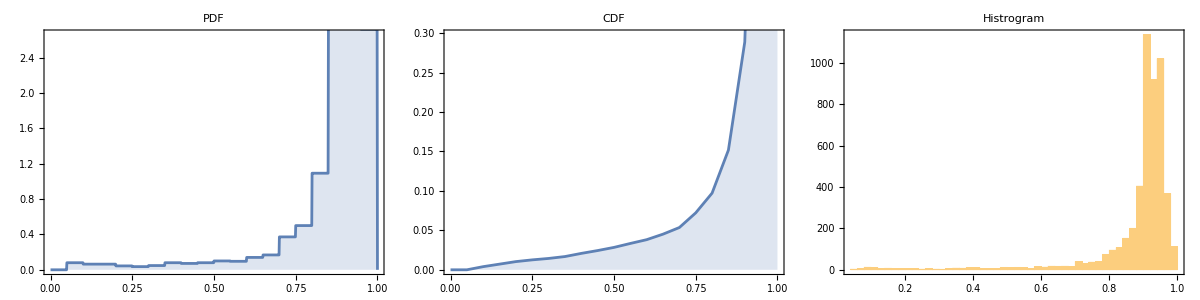

```mathematica
𝒟=HistogramDistribution[Stest2];
Grid[{(DiscretePlot[#[𝒟,x],{x,0,1,0.001},PlotLabel->#,ImageSize->Medium, Frame->True]&/@{PDF,CDF})~Join~{Histogram[Stest2//Chop,50,Frame->True,ImageSize->Medium,PlotLabel->"Histrogram"]}}]
```

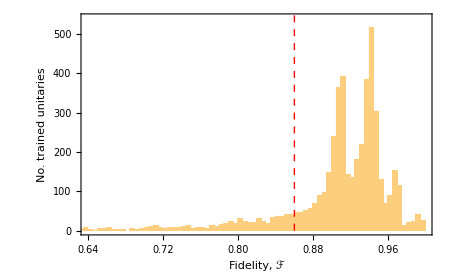

Histogram depicting the deviation of the output fidelities achieved by the unitary operators trained for a double iteration of the protocol by the VQA, which was executed 5000 times. The unitaries were tested on the input state, having an initial fidelity of ℱ_0=0.9125 to the GHZ state (denoted by the red dashed line).

```mathematica
lineStyle={Red,Dashed};
line1=Line[{{cGHZ.ρ0.GHZ,0.},{cGHZ.ρ0.GHZ,2000 cGHZ.ρ0.GHZ}}];
H2=Histogram[Stest2,{0.005},Frame->True,FrameLabel->{"Fidelity, ℱ", "No. trained unitaries"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotRange->{{0.64,1},{0.,540}},Epilog->{Directive[lineStyle],line1},PlotRangeClipping->True]

Text[Style["Histogram depicting the deviation of the output fidelities achieved by the unitary operators trained for a double iteration of the protocol by the VQA, which was executed 5000 times. The unitaries were tested on the input state, having an initial fidelity of ℱ_0=0.9125 to the GHZ state (denoted by the red dashed line).",FontFamily->"CMU Serif",17]]
```

```mathematica
(* success rate of training *)
Νsuc1=Length[Select[Stest2,#>cGHZ.ρ0.GHZ&]]/5000*100//N
```

53.18

```mathematica
(* index of U yields fidelity > 0.99 *)
SidxF2=Flatten[Position[Stest2,Select[Stest2,#>0.996&][[#]]]&/@Range[Length[Select[Stest2,#>0.996&]]]]
```

{21,108,1523,1664,2703,2713,4017,4437,4524,4923}

```mathematica
ρ0′=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
Fs[pars_,R_]:=Block[{},
Transpose[{(Range[R]-1),cGHZ.ItC[ρ0′,pars,#].GHZ&/@(Range[R]-1)//Chop}]]
```

```mathematica
SU2=Fs[#,11]&/@Spms2[[SidxF2]];
```

```mathematica
(*** The protocol reveals a length-two cycle in convergence. ***)
```

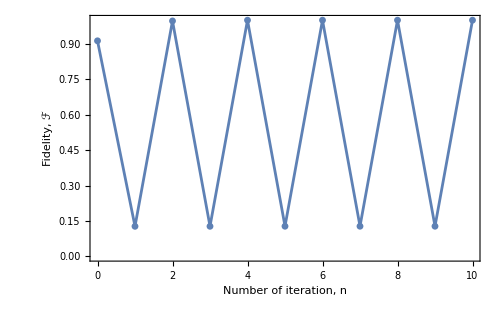

```mathematica
(* best is U10 *)
Fλplot2=ListLinePlot[SU2[[10]],Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->500,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},PlotRange->Full,FrameTicks->{{Automatic,Automatic},{Range[11]-1,Automatic}}]
```

```mathematica
(* function of different noise strengths *)

Fλ[pars_,R_]:=ParallelTable[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.ItC[ρ0,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0.1,0.9,0.2}]
```

```mathematica
Sλ2=Fλ[Spms2[[SidxF2]][[10]],10];
```

```mathematica
(* For guiding the eye, we hide the oscillation behavior and only plot the even-numbered iterations. *)
Sλ2Even=Take[#,{1,-1,2}]&/@Sλ2;
```

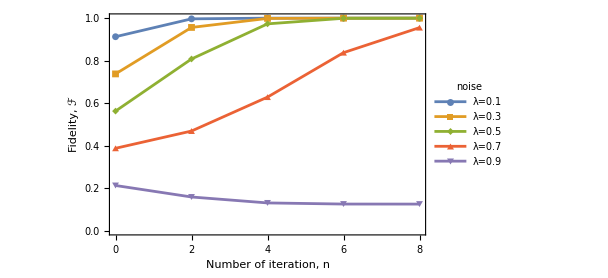

```mathematica
Fλsplot2=ListLinePlot[Sλ2Even,
Frame->True,FrameLabel->{"Number of iteration, n", "Fidelity, ℱ"},ImageSize->450,Axes->False,FrameStyle->Directive[Black],FrameTicks->{{Automatic,Automatic},{Range[11]-1,Automatic}},PlotMarkers->{Automatic,Small},
PlotLegends->Placed[PointLegend[{"λ=0.1","λ=0.3","λ=0.5","λ=0.7","λ=0.9"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&),LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black}],{{0.8,0.1},{0.15,0.01}}],LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black}
]
```

```mathematica
(* ERROR MODEL 1: coherent noise *)
ψe=N@Normalize[Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1]+0.4 Flatten@KroneckerProduct[S0,S1,S1]];
ρe=(1-λ)*SparseArray[Outer[Times, ψe,Conjugate[ψe]]]+λ/8 IdentityMatrix[8]/.λ->0.;
```

```mathematica
ψghzbasis=Flatten[Table[Flatten[KroneckerProduct[Sequence@@{i,j,k}]],{i,{S0,S1}},{j,{S0,S1}},{k,{S0,S1}}],2][[2;;-2]];
ψghzl=N@Normalize[GHZ+ϵ*#]&/@ψghzbasis;
ρghzl=Outer[Times, #,Conjugate[#]]&/@ψghzl;
ψall=N@Normalize[GHZ+ϵ*Total[ψghzbasis]];
ρall=Outer[Times, ψall,Conjugate[ψall]];
```

```mathematica
(* ERROR MODEL 2: GHZ-like initial states *)
ψg=Normalize[Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1]+{-ϵ,0,0,0,0,0,0,ϵ}];
ρg=Outer[Times, ψg,Conjugate[ψg]];
```

```mathematica
(*** FUNCTION OF ITERATIONS ***)
Fe[pars_,R_]:=Block[{},
Transpose[{(Range[R]-1),cGHZ.ItC[ρe,pars,#].GHZ&/@(Range[R]-1)//Chop}]]

Feλ[pars_,R_]:=ParallelTable[Block[{ψe,ρe},
ψe=N@Normalize[Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1]+ϵ Flatten@KroneckerProduct[S0,S1,S1]]/.ϵ->ϵ′;
ρe=SparseArray[Outer[Times, ψe,Conjugate[ψe]]];
Transpose[{(Range[R]-1),cGHZ.ItC[ρe,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{ϵ′,0.1,1.3,0.1}]

FghzL[pars_,R_]:=ParallelTable[Block[{ψe,ρe},
ψe=N@Normalize[Flatten@KroneckerProduct[S0,S0,S0]+ϵ*Flatten@KroneckerProduct[S1,S1,S1]]/.ϵ->ϵ′;
ρe=SparseArray[Outer[Times, ψe,Conjugate[ψe]]];
Transpose[{(Range[R]-1),cGHZ.ItC[ρe,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{ϵ′,0.1,1,0.2}]

FghzBasis[ρ_,pars_,R_]:=Block[{},
Transpose[{(Range[R]-1),cGHZ.ItC[ρ,pars,#].GHZ&/@(Range[R]-1)//Chop}]]

Fall[pars_,R_]:=Block[{},
Transpose[{(Range[R]-1),cGHZ.ItC[ρall,pars,#].GHZ&/@(Range[R]-1)//Chop}]]

Fg[pars_,R_]:=ParallelTable[Block[{ρg′},
ρg′=ρg/.ϵ->ϵ′;
Transpose[{(Range[R]-1),cGHZ.ItC[ρg′,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{ϵ′,-0.5,0.1,0.1}]
```

```mathematica
N@Normalize[Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1]+1 Flatten@KroneckerProduct[S0,S1,S1]]
```

{0.57735,0.,0.,0.57735,0.,0.,0.,0.57735}

```mathematica
(* plot the Fidelity vs interation number for a certain noise level, noise model 1 *)
```

```mathematica
SUE2=Fe[Spms2[[SidxF2]][[10]],11];
SUE2Even=Take[SUE2,{1,-1,2}];
```

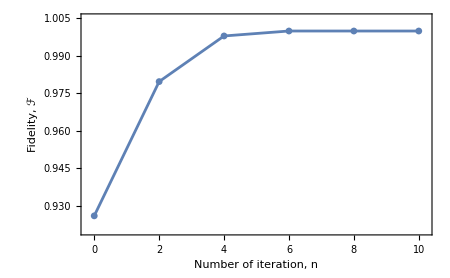

```mathematica
Fϵ2=ListLinePlot[SUE2Even,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},PlotRange->{{-0.2,10.2},{0.92,1.005}},FrameTicks->{{Automatic,Automatic},{Range[11]-1,Automatic}}]
```

```mathematica
(* plot the Fidelity vs interation number for a variaty noise level, noise model 1 *)
```

```mathematica
Se2=Feλ[Spms2[[SidxF2]][[10]],11];
S2ghzl=FghzL[Spms2[[SidxF2]][[10]],11];
```

```mathematica
Se2Even=Take[#,{1,-1,2}]&/@Se2;
S2ghzlEven=Take[#,{1,-1,2}]&/@S2ghzl;
```

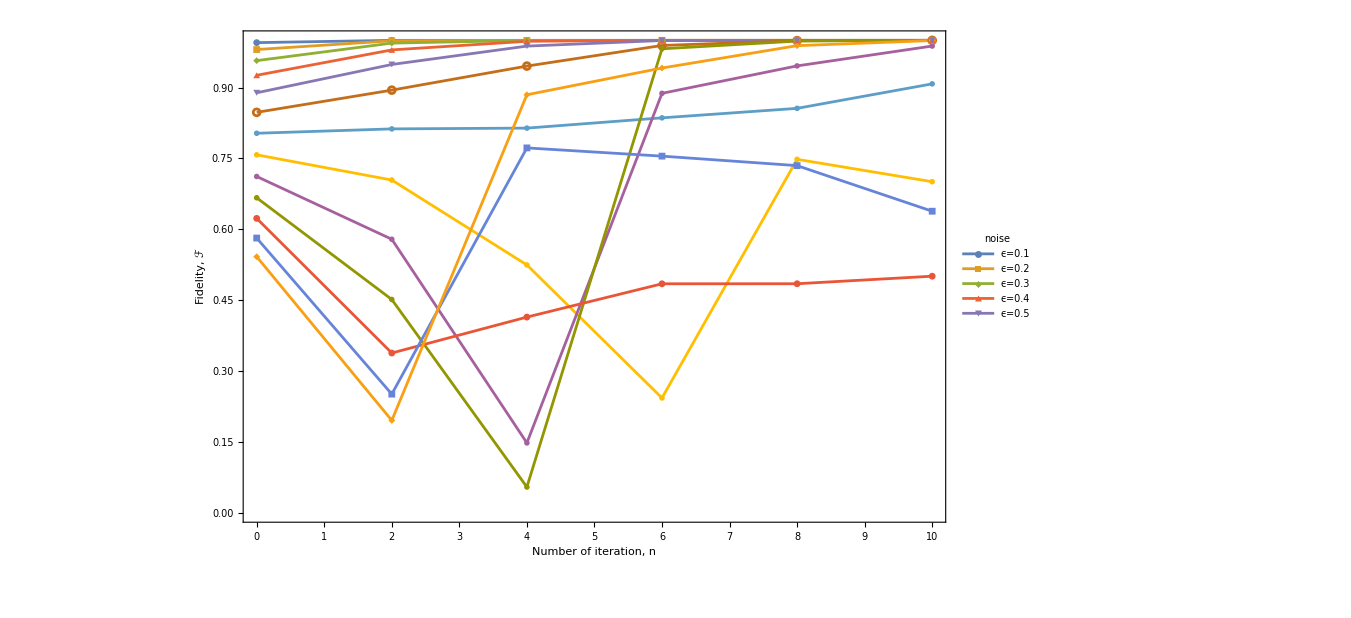

```mathematica
(** chaotic behavior above a certain level of noise **)
Feplot2=ListLinePlot[Se2Even,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->1000,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},PlotRange->All,FrameTicks->{{Automatic,Automatic},{Range[11]-1,Automatic}},
PlotLegends->Placed[PointLegend[{"ϵ=0.1","ϵ=0.2","ϵ=0.3","ϵ=0.4","ϵ=0.5"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.1},{0.15,0.01}}]
]
```

```mathematica
(* plot the Fidelity vs interation number for a variaty noise level, noise model 2 *)
```

```mathematica
Sg2=Fg[Spms2[[SidxF2]][[10]],10];
Sg2Even=Take[#,{1,-1,2}]&/@Sg2;
```

{(1-ϵ)/(√(Abs[1-ϵ]^2+Abs[1+ϵ]^2)),0,0,0,0,0,0,(1+ϵ)/(√(Abs[1-ϵ]^2+Abs[1+ϵ]^2))}

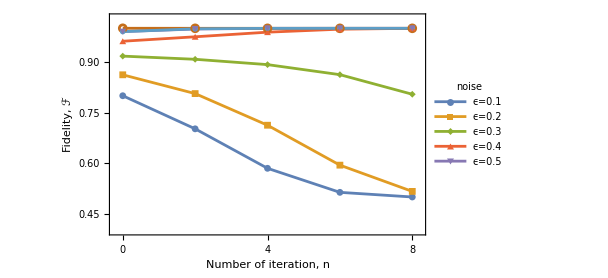

```mathematica
ψg
Sgplot2=ListLinePlot[Sg2Even,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[20]-1,Automatic}},PlotRange->{{-0.2,8.2},{0.4,1.03}},PlotLegends->Placed[PointLegend[{"ϵ=0.1","ϵ=0.2","ϵ=0.3","ϵ=0.4", "ϵ=0.5"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&),LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black}],{{0.8,0.1},{0.15,0.01}}]
]
```

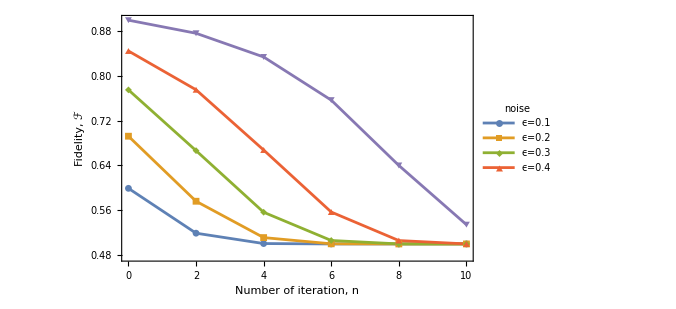

```mathematica
FGHZLplot2=ListLinePlot[S2ghzlEven,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->500,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},PlotRange->Full,FrameTicks->{{Automatic,Automatic},{Range[11]-1,Automatic}},
PlotLegends->Placed[PointLegend[{"ϵ=0.1","ϵ=0.2","ϵ=0.3","ϵ=0.4"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&)],{{0.8,0.17},{0.15,0.01}}]
]
```

```mathematica
SghzBasis=FghzBasis[#,Spms2[[SidxF2]][[10]],11]&/@ρghzl;
```

```mathematica
(***** TABLE OF TRAINED PARAMETERS *****)
```

```mathematica
Grid[{{""}~Join~Table[θ[i],{i,1,8}],{"U_1"}~Join~Round[Mod[Spms2[[SidxF2]][[10]],π],0.01][[1;;8]],{"U_2"}~Join~Round[Mod[Spms2[[SidxF2]][[9]],π],0.01][[1;;8]],{"U_3"}~Join~Round[Mod[Spms2[[SidxF2]][[8]],π],0.01][[1;;8]],
{""}~Join~Table[θ[i],{i,9,16}],{"U_1"}~Join~Round[Mod[Spms2[[SidxF2]][[10]],π],0.01][[9;;-1]],{"U_2"}~Join~Round[Mod[Spms2[[SidxF2]][[9]],π],0.01][[9;;-1]],{"U_3"}~Join~Round[Mod[Spms2[[SidxF2]][[8]],π],0.01][[9;;-1]]},Frame->All]
```

| θ[1] | θ[2] | θ[3] | θ[4] | θ[5] | θ[6] | θ[7] | θ[8]
U_1 | 3.1 | 1.83 | 0. | 1.13 | 0.56 | 1.67 | 3.05 | 1.56
U_2 | 3.05 | 1.87 | 3.1 | 1.84 | 2.53 | 0.93 | 3.1 | 1.95
U_3 | 1.49 | 0.87 | 3.07 | 1.21 | 1.56 | 1.56 | 2.28 | 1.5
 | θ[9] | θ[10] | θ[11] | θ[12] | θ[13] | θ[14] | θ[15] | θ[16]
U_1 | 3.14 | 2.37 | 3.04 | 2.49 | 1.81 | 2.9 | 0.2 | 3.11
U_2 | 0.03 | 3.03 | 1.54 | 1.55 | 1.25 | 0.61 | 1.6 | 3.09
U_3 | 3.14 | 0.77 | 2.37 | 1.63 | 2.08 | 1.51 | 2.46 | 2.97

```mathematica
(* Initial set is symmetric thus can be refined to the range(0,π) *)
```

```mathematica
Spms2[[SidxF2]][[10]]
Mod[Spms2[[SidxF2]][[10]],π]
Mod[Spms2[[SidxF2]][[10]],2 π]
```

{6.23933,1.83399,0.00408233,4.26858,3.70372,1.67332,-0.0898672,4.70203,3.13774,5.50861,-0.100535,5.63053,1.81092,2.90356,3.34254,6.24678}

{3.09774,1.83399,0.00408233,1.12699,0.56213,1.67332,3.05173,1.56044,3.13774,2.36702,3.04106,2.48894,1.81092,2.90356,0.200945,3.10518}

{6.23933,1.83399,0.00408233,4.26858,3.70372,1.67332,6.19332,4.70203,3.13774,5.50861,6.18265,5.63053,1.81092,2.90356,3.34254,6.24678}

```mathematica
Feλ[Spms2[[SidxF2]][[10]],1][[All,All,2]]
Feλ[Mod[Spms2[[SidxF2]][[10]],π],1][[All,All,2]]
Feλ[Mod[Spms2[[SidxF2]][[10]],2 π],1][[All,All,2]]
```

{{0.995025},{0.980392},{0.956938},{0.925926},{0.888889}}

{{0.995025},{0.980392},{0.956938},{0.925926},{0.888889}}

{{0.995025},{0.980392},{0.956938},{0.925926},{0.888889}}

#### Analyzing trained U for single iteration, while λ has been varied in range(0.05-0.3)

```mathematica
(* joined 5000 trained parameters *)
Spms1=sdata it1 3~Join~sdata it1 4~Join~sdata it1 5~Join~sdata it1 6~Join~sdata it1 7~Join~sdata it1 8~Join~sdata it1 9~Join~sdata it1 10~Join~sdata it1 11~Join~sdata it1 12;
```

```mathematica
(* testing their performance on a certain initial state *)
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
Stest1=Chop[cGHZ.ItC[ρ0,#1,1].GHZ&/@Spms1];
(*Stest1 it2=Chop[loss[#1,ρ0]&/@Spms1];*)
```

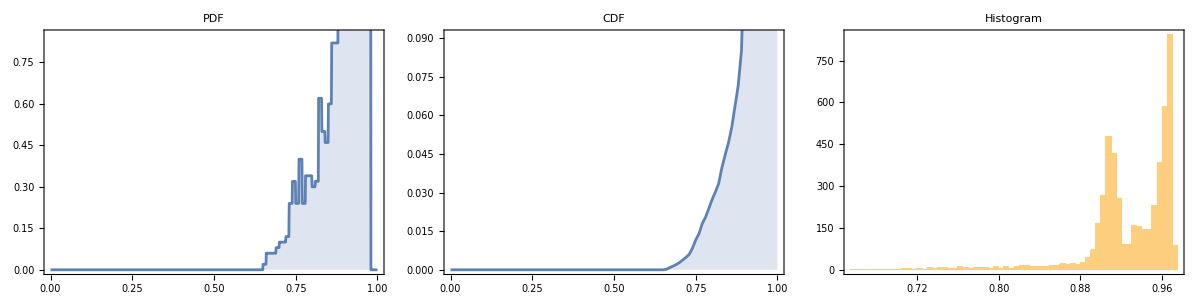

```mathematica
𝒟=HistogramDistribution[Stest1];
Grid[{(DiscretePlot[#[𝒟,x],{x,0,1,0.001},PlotLabel->#,ImageSize->Medium, Frame->True]&/@{PDF,CDF})~Join~{Histogram[Stest1//Chop,50,Frame->True,ImageSize->Medium,PlotLabel->"Histogram"]}}]
```

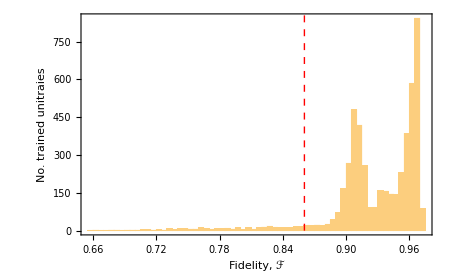

Histogram depicting the deviation of the output fidelities achieved by the unitary operators trained for a single iteration of the protocol by the VQA, which was executed 5000 times. The unitaries were tested on the input state, having an initial fidelity of ℱ_0=0.9125 to the GHZ state (denoted by the red dashed line).

```mathematica
lineStyle={Red,Dashed};
line1=Line[{{cGHZ.ρ0.GHZ,0.},{cGHZ.ρ0.GHZ,2000 cGHZ.ρ0.GHZ}}];
H1=Histogram[Stest1,{0.005},Frame->True,FrameLabel->{"Fidelity, ℱ", "No. trained unitraies"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotRange->{{All,1},{0.,All}},Epilog->{Directive[lineStyle],line1}]

Text[Style["Histogram depicting the deviation of the output fidelities achieved by the unitary operators trained for a single iteration of the protocol by the VQA, which was executed 5000 times. The unitaries were tested on the input state, having an initial fidelity of ℱ_0=0.9125 to the GHZ state (denoted by the red dashed line).",FontFamily->"CMU Serif",17]]
```

```mathematica
(* success rate of training *)
Νsuc1=Length[Select[Stest1,#>cGHZ.ρ0.GHZ&]]/5000*100//N
```

66.14

```mathematica
(* index of U yields fidelity > 0.97 *)
SidxF1=Flatten[Position[Stest1,Select[Stest1,#>0.97&][[#]]]&/@Range[Length[Select[Stest1,#>0.97&]]]]
```

{18,41,64,89,110,139,168,225,418,444,524,541,665,727,830,853,907,941,947,1097,1102,1291,1471,1486,1514,1523,1590,1595,1598,1681,1762,1803,1824,1845,1859,1894,1965,1966,1981,2007,2046,2211,2228,2313,2483,2517,2523,2525,2673,2697,2722,2841,2936,2967,3048,3121,3188,3216,3218,3231,3253,3301,3303,3333,3511,3523,3568,3620,3660,3669,3797,3806,3816,3967,3968,4050,4088,4224,4238,4300,4425,4437,4447,4484,4531,4632,4720}

```mathematica
ρ0′=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
Fs[pars_,R_]:=Block[{},
Transpose[{(Range[R]-1),cGHZ.ItC[ρ0′,pars,#].GHZ&/@(Range[R]-1)//Chop}]]
```

```mathematica
SU1=Fs[#,10]&/@Spms1[[SidxF1]];
```

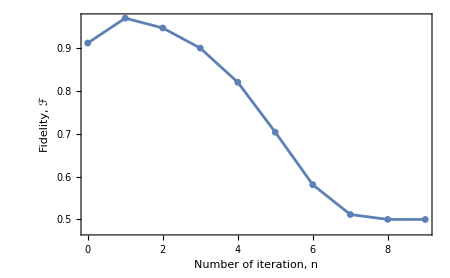

```mathematica
(* best performance on testing data achieved by U82,83,84 *)
Fλplot1=ListLinePlot[SU1[[82]],Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->Full]
```

```mathematica
(* function of different noise strengths *)

Fλ[pars_,R_]:=ParallelTable[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.ItC[ρ0,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0.1,0.5,0.1}]
```

```mathematica
Sλ1=Fλ[#,5]&/@Spms1[[SidxF1]];
```

```mathematica
Sλ1′=Fλ[Spms1[[SidxF1]][[82]],8];
```

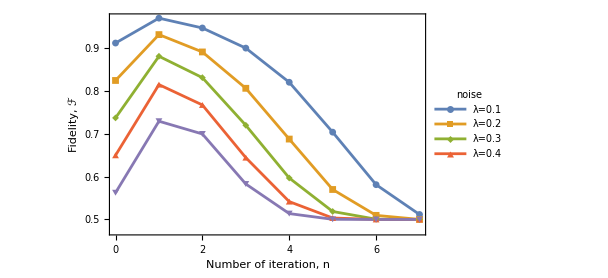

```mathematica
Fλsplot1=ListLinePlot[Sλ1′,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->Full,PlotLegends->Placed[PointLegend[{"λ=0.1","λ=0.2","λ=0.3","λ=0.4"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&),LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black}],{{0.81,0.42},{0.15,0.01}}]
]
```

```mathematica
(*** TABLE OF TRANINED PARAMETERS ***)
```

```mathematica
Grid[{{""}~Join~Table[θ[i],{i,1,8}],{"U_1"}~Join~Round[Mod[Spms1[[SidxF1]][[82]],π],0.01][[1;;8]],{"U_2"}~Join~Round[Mod[Spms1[[SidxF1]][[83]],π],0.01][[1;;8]],{"U_3"}~Join~Round[Mod[Spms1[[SidxF1]][[84]],π],0.01][[1;;8]],
{""}~Join~Table[θ[i],{i,9,16}],{"U_1"}~Join~Round[Mod[Spms1[[SidxF1]][[82]],π],0.01][[9;;-1]],{"U_2"}~Join~Round[Mod[Spms1[[SidxF1]][[83]],π],0.01][[9;;-1]],{"U_3"}~Join~Round[Mod[Spms1[[SidxF1]][[84]],π],0.01][[9;;-1]]},Frame->All]
```

| θ[1] | θ[2] | θ[3] | θ[4] | θ[5] | θ[6] | θ[7] | θ[8]
U_1 | 1.59 | 0.29 | 2.69 | 2.77 | 0.05 | 2.63 | 2.72 | 0.11
U_2 | 0.07 | 1.46 | 0.58 | 1.27 | 0.88 | 1.9 | 0.56 | 0.19
U_3 | 2.97 | 1.92 | 3.03 | 1.5 | 3.13 | 1.28 | 1.6 | 2.26
 | θ[9] | θ[10] | θ[11] | θ[12] | θ[13] | θ[14] | θ[15] | θ[16]
U_1 | 1.65 | 0.54 | 1.25 | 1.24 | 3.14 | 3.03 | 1.87 | 3.14
U_2 | 0.09 | 3.03 | 2.81 | 0.64 | 2.25 | 2.4 | 0.41 | 2.95
U_3 | 0.16 | 1.04 | 0.11 | 0.02 | 0. | 2.95 | 1.61 | 3.02

```mathematica
(* ERROR MODEL 1: coherent noise *)
ψe=N@Normalize[Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1]+0.4 Flatten@KroneckerProduct[S0,S1,S1]];
ρe=(1-λ)*SparseArray[Outer[Times, ψe,Conjugate[ψe]]]+λ/8 IdentityMatrix[8]/.λ->0.;
```

```mathematica
Fe[pars_,R_]:=Block[{},
Transpose[{(Range[R]-1),cGHZ.ItC[ρe,pars,#].GHZ&/@(Range[R]-1)//Chop}]]

Feλ[pars_,R_]:=ParallelTable[Block[{ψe,ρe},
ψe=N@Normalize[Flatten@KroneckerProduct[S0,S0,S0]+Flatten@KroneckerProduct[S1,S1,S1]+ϵ Flatten@KroneckerProduct[S0,S1,S1]]/.ϵ->ϵ′;
ρe=SparseArray[Outer[Times, ψe,Conjugate[ψe]]];
Transpose[{(Range[R]-1),cGHZ.ItC[ρe,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{ϵ′,1,1.1,0.01}]
```

```mathematica
SUE1=Fe[Spms1[[SidxF1]][[82]],7];
```

```mathematica
Se1=Feλ[Spms1[[SidxF1]][[82]],8];
```

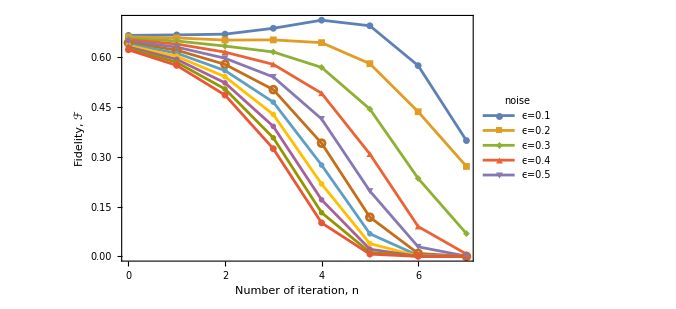

```mathematica
Se1plot=ListLinePlot[Se1,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->500,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->All,PlotLegends->Placed[PointLegend[{"ϵ=0.1","ϵ=0.2","ϵ=0.3","ϵ=0.4", "ϵ=0.5"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&)],{{0.12,0.05},{0.2,0.01}}]
]
```

```mathematica
(* ERROR MODEL 2.: GHZ-like initial state *)
```

```mathematica
Sg=Fg[Spms1[[SidxF1]][[82]],8];
```

{(1-ϵ)/(√(Abs[1-ϵ]^2+Abs[1+ϵ]^2)),0,0,0,0,0,0,(1+ϵ)/(√(Abs[1-ϵ]^2+Abs[1+ϵ]^2))}

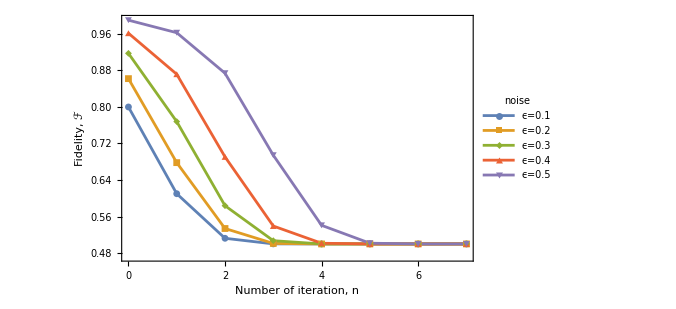

```mathematica
ψg
Sgplot=ListLinePlot[Sg,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->500,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->All,PlotLegends->Placed[PointLegend[{"ϵ=0.1","ϵ=0.2","ϵ=0.3","ϵ=0.4", "ϵ=0.5"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&)],{{0.82,0.05},{0.2,0.01}}]
]
```

```mathematica
SghzBasis1=FghzBasis[#,Spms1[[SidxF1]][[82]],7]&/@SparseArray[ρghzl/.ϵ->0.4];
```

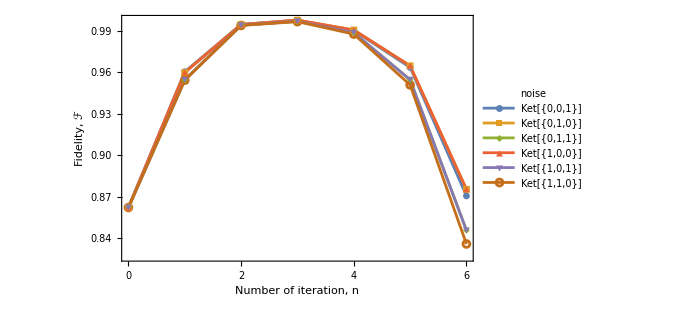

```mathematica
BasisEplot1=ListLinePlot[SghzBasis1,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->14,Black},ImageSize->500,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->All,PlotLegends->Placed[PointLegend[Ket[#]&/@Tuples[{0,1},3][[2;;-2]],LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&)],{{0.12,0.05},{0.2,0.01}}]
]
```

#### Referee review answers

Taking three- or longer iteration protocols does not significantly improve the output fidelity compared to the double-iteration protocol. To confirm this statement, we show the following results.

Training for iteration 3

```mathematica
Spms3=par1 it3~Join~par2 it3~Join~par3 it3~Join~par4 it3~Join~par5 it3;
```

```mathematica
(* testing *)
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
Stest3=Chop[loss[#1,ρ0]&/@Spms3];
```

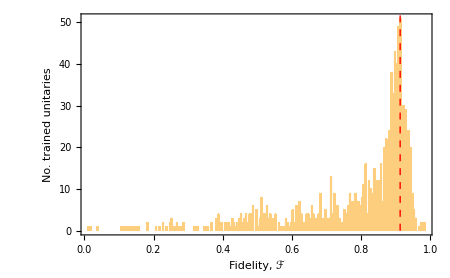

```mathematica
(* note: dont forget to re-set the iteratio number on the loss function *)
lineStyle={Red,Dashed};
line1=Line[{{cGHZ.ρ0.GHZ,0.},{cGHZ.ρ0.GHZ,2000 cGHZ.ρ0.GHZ}}];
H3=Histogram[Stest3,{0.005},Frame->True,Frame->True,FrameLabel->{"Fidelity, ℱ","No. trained unitaries"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotRange->{{0.64,1},{0.,All}},Epilog->{Directive[lineStyle],line1},PlotRangeClipping->True]
```

```mathematica
(* index of U yields fidelity > 0.97 *)
SidxF3=Flatten[Position[Stest3,Select[Stest3,#>0.98&][[#]]]&/@Range[Length[Select[Stest3,#>0.98&]]]]
```

{27,792}

```mathematica
(*noise strength*)

Fλ[pars_,R_]:=ParallelTable[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.ItC[ρ0,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0.1,0.9,0.2}]
```

```mathematica
Sλ3′=Fλ[Spms3[[SidxF3]][[1]],10];
```

```mathematica
Fλsplot3=ListLinePlot[Sλ3′,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->18,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->Full,PlotStyle->Dashed
];

(*PlotLegends->Placed[PointLegend[{"λ=0.1","λ=0.3","λ=0.5","λ=0.7","λ=0.9"},LegendLabel->"noise",LegendFunction->(Framed[#,Background->White]&)],{{0.78,0.1},{0.15,0.01}}]*)
```

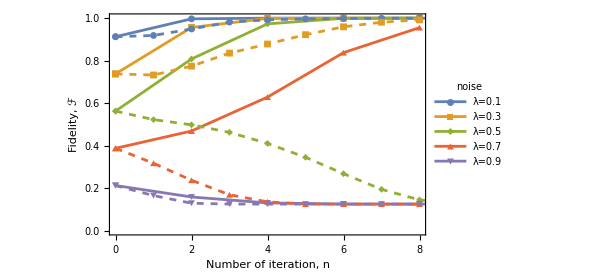

```mathematica
Show[Fλsplot2,Fλsplot3]
```

The training procedure was carried out using the cost fidelity function containing three protocol iterations. It can be seen from the figure that the obtained most-optimal unitary matrix does not give better fidelities (dashed lines) than the unitary matrix trained over two protocol iterations (solid lines).

Training for iteration 4

```mathematica
Spms4=par1 it4~Join~par2 it4~Join~par3 it4~Join~par4 it4~Join~par5 it4;
```

```mathematica
(* testing *)
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
Stest4=Chop[loss[#1,ρ0]&/@Spms4];
```

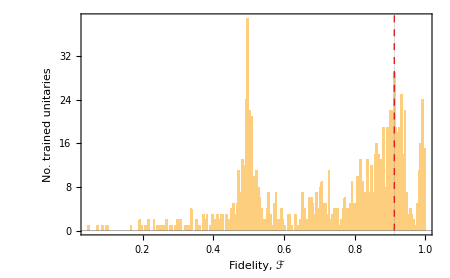

```mathematica
lineStyle={Red,Dashed};
line1=Line[{{cGHZ.ρ0.GHZ,0.},{cGHZ.ρ0.GHZ,2000 cGHZ.ρ0.GHZ}}];
H4=Histogram[Stest4,{0.005},Frame->True,Frame->True,FrameLabel->{"Fidelity, ℱ", "No. trained unitaries"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotRange->{{All,1},{0.,All}},
GridLines->{{0,0,cGHZ.ρ0.GHZ},{0,0,0}},Epilog->{Directive[lineStyle],line1}]
```

```mathematica
(* index of U yields fidelity > 0.97 *)
SidxF4=Flatten[Position[Stest4,Select[Stest4,#>0.9995&][[#]]]&/@Range[Length[Select[Stest4,#>0.9995&]]]]
```

{234}

```mathematica
(*noise strength*)

Fλ[pars_,R_]:=ParallelTable[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.ItC[ρ0,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0.1,0.9,0.2}]
```

```mathematica
Sλ4′=Fλ[Spms4[[SidxF4]][[1]],10];
```

```mathematica
Sλ4Even=Take[#,{1,-1,2}]&/@Sλ4′;
```

```mathematica
Fλsplot4=ListLinePlot[Sλ4Even,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->18,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->Full,PlotStyle->Dashed
];
```

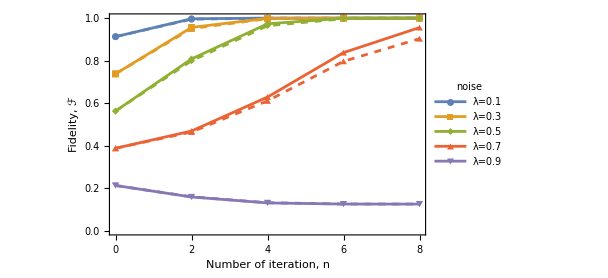

```mathematica
Show[Fλsplot4,Fλsplot2]
```

The training process was carried out using the cost fidelity function, containing four protocol iterations. It can be seen that the obtained most optimal unitary matrix (dashed lines) gives almost the same fidelities as the unitary matrix trained over two protocol iterations (solid lines), but it does not outperform it for any of the inputs.

Motivation of the choice of δ and α parameters

```mathematica
lambs=RandomReal[{0.05,0.3},150];
thetas=RandomReal[{0,2π},16];
```

```mathematica
val listfix={};
paramsfix={};
```

```mathematica
GetValueGrad[f_,pars_,ρ0_]:=Block[{δ=0.01},
f0=f[pars,ρ0];
grad=ParallelMap[(f[pars+#,ρ0]-f0)/δ&,δ IdentityMatrix[Length[pars]]];
{f0,grad}]
```

```mathematica
SGDλ[f_,pars0_,niter_]:=Block[{α=0.1,pars=pars0},
pars list={};
val list={};

Do[
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->lambs[[n]];
{f0,grad}=GetValueGrad[f,pars,ρ0];
AppendTo[pars list,pars];
AppendTo[val list,f0];
pars+=α grad
,{n,niter}];
f[pars,ρ0]]
```

```mathematica
Do[
Block[{},
fid=SGDλ[loss,thetas,150]]//Chop;
AppendTo[val listfix,val list];
AppendTo[paramsfix,pars list//Chop],
1]//Timing
```

{5.57831,Null}

```mathematica
(*SaveToCell[val listfix]*)
```

```mathematica
valslist="data";
```

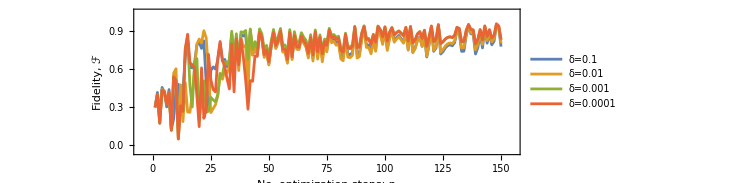

```mathematica
trendδ=ListPlot[val listfix,AspectRatio->1/3,ImageSize->550,Frame->True,PlotRange->{{-5,155},{-0.05,1.05}},FrameLabel->{"No. optimization steps; n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->550,Axes->False,FrameStyle->Directive[Black],Joined->True,PlotLegends->{"δ=0.1","δ=0.01","δ=0.001","δ=0.0001"}]

(*Export["/Users/aronrozgonyi/Documents/PhD/VQA/review/trend_delta.pdf",trendδ]*)
```

```mathematica
αlist={};
```

```mathematica
SGDλ[f_,pars0_,niter_]:=Block[{α=0.001,pars=pars0},
pars list={};
val list={};

Do[
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->lambs[[n]];
{f0,grad}=GetValueGrad[f,pars,ρ0];
AppendTo[pars list,pars];
AppendTo[val list,f0];
pars+=α grad
,{n,niter}];
f[pars,ρ0]]
```

```mathematica
Do[
Block[{},
fid=SGDλ[loss,thetas,150]]//Chop;
AppendTo[αlist,val list];,
1]//Timing
```

{5.41079,Null}

```mathematica
SaveToCell[αlist]
```

```mathematica
(*δ=0.01, "α=1","α=0.1","α=0.01","α=0.001"*)
Savedαlist2="data";
```

```mathematica
(*δ=0.01, "α=1","α=0.1","α=0.01","α=0.001","α=0.0001","α=0.00001"*)
Savedαlist="data";
```

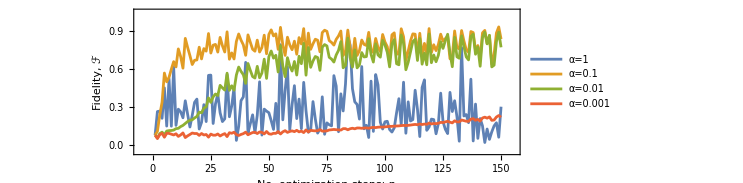

```mathematica
trendα=ListPlot[αlist,AspectRatio->1/3,ImageSize->550,Frame->True,PlotRange->{{-5,155},{-0.05,1.05}},FrameLabel->{"No. optimization steps; n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->550,Axes->False,FrameStyle->Directive[Black],Joined->True,PlotLegends->{"α=1","α=0.1","α=0.01","α=0.001"}]

(*Export["/Users/aronrozgonyi/Documents/PhD/VQA/review/trend_alpha.pdf",trendα]*)
```

Choosing the learning rate is challenging as a value too small may result in a long training process that could get stuck, whereas setting your learning rate too high, your model’s convergence will be unstable; training loss may bounce around, or even get stuck at a suboptimal level (local minima). According to our results, choosing value α = 0.1 is a reasonable choice.

Training the circuit with ansatz including a single CNOT gate

GHZ distillation can be realized even with some smaller ansatz.  To demonstrate this statement, we have performed the following simulation:  Instead of the ansatz plotted in Fig. 2., we considered another ansatz containing only  8 single-qubit gates and a single CNOT gate. We performed the optimization with this smaller quantum circuit, which contains only 8 variational parameters.  In the figure below, the dashed lines correspond to the best unitary found with a 1-CNOT quantum circuit, while the continuous lines correspond to the original ansatz.

```mathematica
(*** FUNCTIONS FOR SINGLE CNOT CIRCUIT ANSATZ ***)

(* 1-cnot quantum circuit and 0-measurement *)
SingleCXCircuit[ρ0_,{θ0_,θ1_,θ2_,θ3_,θ4_,θ5_,θ6_,θ7_},n_]:=Block[{U,ρM,ρ,ρ00},
ρ00=SparseArray[KroneckerProduct[ρ0,ρ0]];
U=SparseArray[KroneckerProduct[Rθ[θ4,X].Rθ[θ5,Z],Rθ[θ4,X].Rθ[θ5,Z],Rθ[θ4,X].Rθ[θ5,Z],Rθ[θ6,X].Rθ[θ7,Z],Rθ[θ6,X].Rθ[θ7,Z],Rθ[θ6,X].Rθ[θ7,Z]]].CXs.SparseArray[KroneckerProduct[Rθ[θ0,X].Rθ[θ1,Z],Rθ[θ0,X].Rθ[θ1,Z],Rθ[θ0,X].Rθ[θ1,Z],Rθ[θ2,X].Rθ[θ3,Z],Rθ[θ2,X].Rθ[θ3,Z],Rθ[θ2,X].Rθ[θ3,Z]]];
;
ρ=U.ρ00.ConjugateTranspose[U];
ρM=M′.ρ;
PartialTrace[ρM,{4,5,6}]
]

(* iterations of protocol *)
IterSCX[ρ0_,pars_,n_]:=Block[{ρ},ρ=Fold[#/Tr[#]&@SingleCXCircuit[#1,pars,#2]&,ρ0,Range[n]]]

(* loss function - fidelity with GHZ state *)
lossSCX[pars_,ρ0_]:=cGHZ.IterSCX[ρ0,pars,2].GHZ
```

```mathematica
his list={};
params={};
Do[
Block[{pars0},
pars0=RandomReal[{0,2π},8];
fid=StochasticGradientDescent[lossSCX,pars0,150]]//Chop;
AppendTo[his list,fid];
AppendTo[params,pars list⟦-1⟧//Chop],
600]//Timing
```

{2113.19,Null}

```mathematica
(*SaveToCell[params]*)
```

```mathematica
parSCXit2 3="data";
```

```mathematica
parSCXit2 2="data";
```

```mathematica
parSCXit2 1="data";
```

```mathematica
(* testing *)
SpSCXit2=parSCXit2 1~Join~parSCXit2 2~Join~parSCXit2 3;

ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
SCXtestit2=Chop[lossSCX[#1,ρ0]&/@SpSCXit2];
```

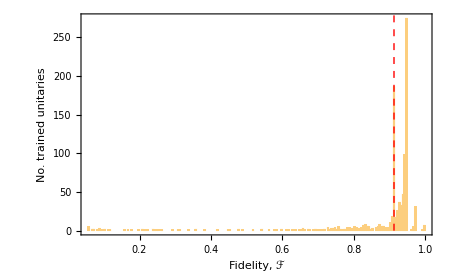

```mathematica
lineStyle={Red,Dashed};
line1=Line[{{cGHZ.ρ0.GHZ,0.},{cGHZ.ρ0.GHZ,2000 cGHZ.ρ0.GHZ}}];
HSCX=Histogram[SCXtestit2,{0.005},Frame->True,FrameLabel->{"Fidelity, ℱ", "No. trained unitaries"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotRange->{{0.64,1},{0.,All}},Epilog->{Directive[lineStyle],line1},PlotRangeClipping->True]
```

```mathematica
(* index of U yields fidelity > 0.97 *)
SCXidxF2=Flatten[Position[SCXtestit2,Select[SCXtestit2,#>0.995&][[#]]]&/@Range[Length[Select[SCXtestit2,#>0.995&]]]]
```

{20,38,339,441,508,516,950}

```mathematica
(*noise strength*)

FλSCX[pars_,R_]:=ParallelTable[Block[{ρ0},
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->λ′;
Transpose[{(Range[R]-1),cGHZ.IterSCX[ρ0,pars,#].GHZ&/@(Range[R]-1)//Chop}]],{λ′,0.1,0.9,0.2}]
```

```mathematica
SCXλ2=FλSCX[SpSCXit2[[SCXidxF2]][[6]],10];
SCXλ2Even=Take[#,{1,-1,2}]&/@SCXλ2;
```

```mathematica
FλSCXplot2=ListLinePlot[SCXλ2Even,Frame->True,FrameLabel->{"Number of iteration, n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->18,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotMarkers->{Automatic,Small},FrameTicks->{{Automatic,Automatic},{Range[10]-1,Automatic}},PlotRange->Full,PlotStyle->Dashed
];
```

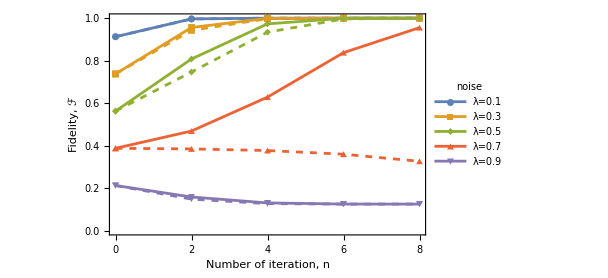

```mathematica
Show[FλSCXplot2,Fλsplot2]
```

This result proves that GHZ distillation can be achieved even with a smaller ansatz. However, as we can see in the above figure, the resulting circuit leads to slower convergence and lower critical noise (as suggested by the curves lambda=0.7 and lambda=0.5).

Smaller range for noise strength in training

```mathematica
(*SaveToCell[parλ2]*)
```

```mathematica
parλ2="data";
```

```mathematica
(* testing *)
ρ0=(1-λ)*ρGHZ+λ/8 IdentityMatrix[8]/.λ->0.1;
Stestλ=Chop[loss[#1,ρ0]&/@parλ2];
```

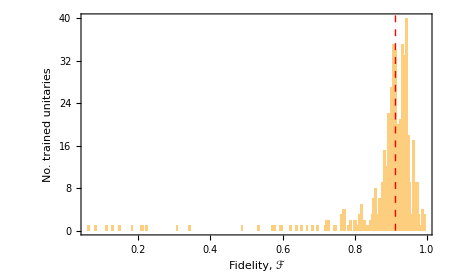

```mathematica
lineStyle={Red,Dashed};
line1=Line[{{cGHZ.ρ0.GHZ,0.},{cGHZ.ρ0.GHZ,200 cGHZ.ρ0.GHZ}}];
Hsl=Histogram[Stestλ,{0.005},Frame->True,FrameLabel->{"Fidelity, ℱ", "No. trained unitaries"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],PlotRange->{{All,1},{0.,All}},Epilog->{Directive[lineStyle],line1}]
```

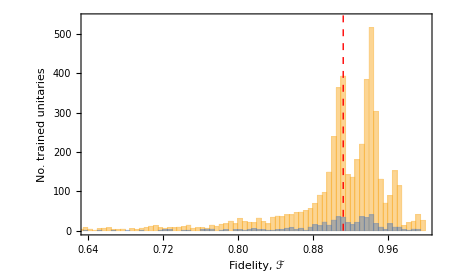

```mathematica
Histogram[{Stest2,Stestλ},{0.005},Frame->True,FrameLabel->{"Fidelity, ℱ", "No. trained unitaries"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->450,Axes->False,FrameStyle->Directive[Black],Epilog->{Directive[lineStyle],line1},PlotRange->{{0.64,1},{0.,540}},PlotRangeClipping->True]
```

It doesn’t yield the disappearance of the double peak in the distribution.

Trend of the cost function during the optimization

```mathematica
vals={};
Do[
Block[{pars0},
pars0=RandomReal[{0,2π},16];
fid=StochasticGradientDescent[loss,pars0,300]]//Chop;
AppendTo[vals,val list],
15]//Timing
```

{163.199,Null}

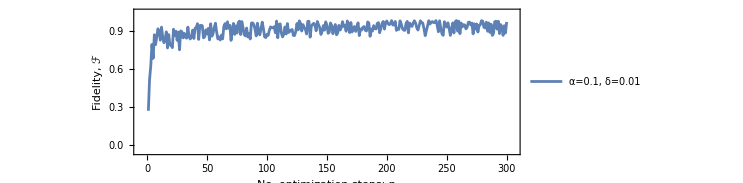

```mathematica
ListPlot[val list,AspectRatio->1/3,ImageSize->550,Frame->True,PlotRange->{{-5,305},{-0.05,1.05}},FrameLabel->{"No. optimization steps; n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->550,Axes->False,FrameStyle->Directive[Black],Joined->True,PlotLegends->{"α=0.1,\nδ=0.01"}]
```

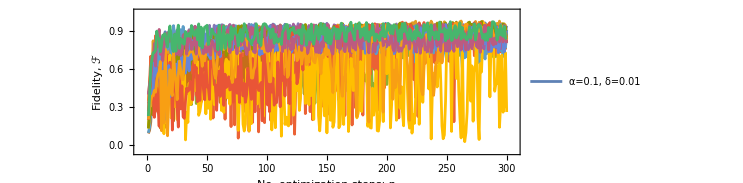

```mathematica
ListPlot[vals[[1;;15]],AspectRatio->1/3,ImageSize->550,Frame->True,PlotRange->{{-5,305},{-0.05,1.05}},FrameLabel->{"No. optimization steps; n","Fidelity, ℱ"},LabelStyle->{FontFamily->"CMU Serif",FontSize->17,Black},ImageSize->550,Axes->False,FrameStyle->Directive[Black],Joined->True,PlotLegends->{"α=0.1,\nδ=0.01"}]
```

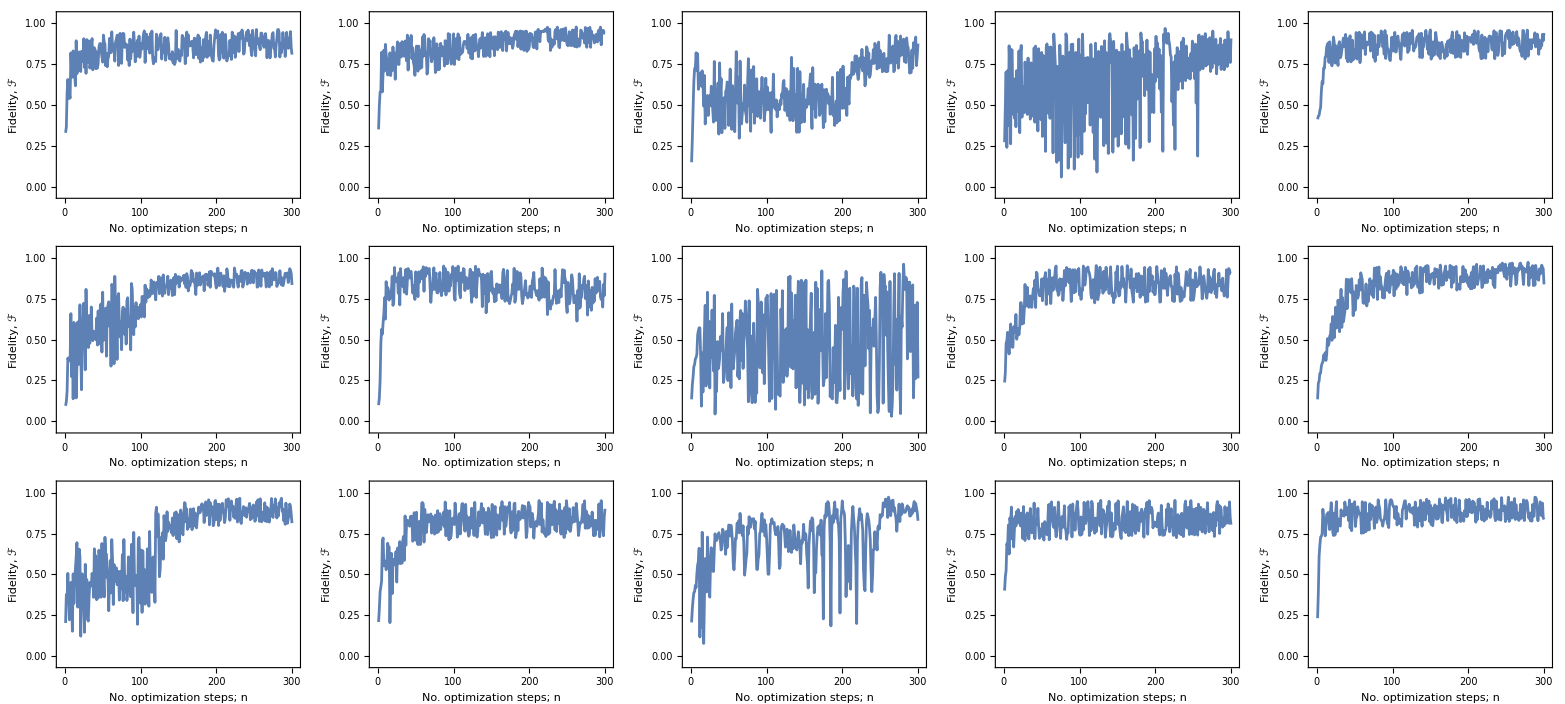

```mathematica
gr=ListPlot[#,AspectRatio->1/3,Frame->True,PlotRange->{{-5,305},{-0.05,1.05}},FrameLabel->{"No. optimization steps; n","Fidelity, ℱ"},Axes->False,FrameStyle->Directive[Black],Joined->True,ImageSize->265]&/@vals;

Grid[{gr[[1;;5]],gr[[6;;10]],gr[[11;;15]]},Frame->All]
```